Suppose mu is a root for x^3+x+s (1-x^2)=0, solve for corresponding s, and then plug-in x^3+x+s (1-x^2)

```mathematica
p[s_,x_]:=x^3+x+s (1-x^2)
Factor[p[s,x]/.Solve[p[s,mu]==0,s][[1]]]
```

((-mu+x) (-1-mu^2-2 mu x-x^2+mu^2 x^2))/((-1+mu) (1+mu))

{x→0.2}

{x→-0.208333+1.01977 ⅈ}

{x→-0.208333-1.01977 ⅈ}

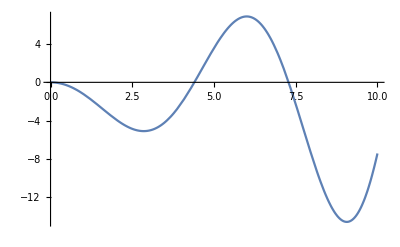

```mathematica
g[x_]:=Factor[p[s,x]/.Solve[p[s,mu]==0,s][[1]]]*(-1+mu) (1+mu)
slo=Solve[g[x]==0,x]/.mu-> 0.2;
a1=slo[[1]]
a2=slo[[2]]
a3=slo[[3]]
f[L_]:=FullSimplify[Det[{{1,1,1},{x/.a1,x/.a2,x/.a3},{E^(-x  L)/.a1,E^(-x L)/.a2,E^(-x L)}/.a3}]]/I
Plot[f[L],{L,0,10}]
```

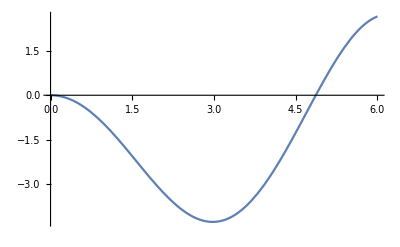

```mathematica
f[L_]:=FullSimplify[Det[{{1,1,1},{x/.a1,x/.a2,x/.a3},{E^(-x  L)/.a1,E^(-x L)/.a2,E^(-x L)}/.a3}]]/I
Plot[f[L],{L,0,6}]
```

(-2 ⅇ^(-L mu) mu^2 √(-1+mu^2+mu^4)+(ⅇ^((L (-mu+√(-1+mu^2+mu^4)))/(-1+mu^2)) (mu-√(-1+mu^2+mu^4))^2 (2 mu-mu^3+√(-1+mu^2+mu^4)))/((-1+mu^2)^2)+(ⅇ^(-(L (mu+√(-1+mu^2+mu^4)))/(-1+mu^2)) (mu+√(-1+mu^2+mu^4))^2 (-2 mu+mu^3+√(-1+mu^2+mu^4)))/((-1+mu^2)^2))/(1-mu^2)

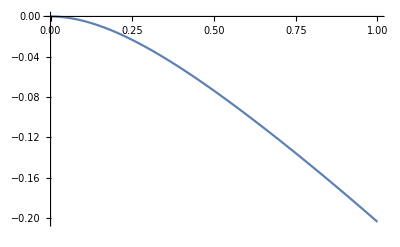

```mathematica
g[x_]:=Factor[p[s,x]/.Solve[p[s,mu]==0,s][[1]]]*(-1+mu) (1+mu)
slo=Solve[g[x]==0,x];
a1=slo[[1]];
a2=slo[[2]];
a3=slo[[3]];
h[L_]:=FullSimplify[Det[{{1,1,1},{x/.a1,x/.a2,x/.a3},{E^(-x  L)/.a1,E^(-x L)/.a2,E^(-x L)}/.a3}]]
Simplify[h''[L]]
```

```mathematica
2Pi/3//N
```

2.0944

```mathematica
x/.a1
```

2